# Projekt 2 - Normal Distribution

## KTH/ICT:IX1501 - Statistics

Joe Huldén, joeda@kth.se
Gustav Wiiala, wiiala@kth.se

KTH/ICT - Communication Systems

2015-12-03

## Det relativa felet av Normal Approximation

### Projekt 2 Situation: Antag att genomsnittet av 20 oberoende .s.v., normal fördelningen anses vara en god approximation. Hur som helst, i den här uppgiften kommer vi att gå bortom den rekommendationen och studera under vilken omständighet det är giltig. Exponential fördelningen är väldig skew jämförd med likformig fördelningen. Hur påverkar detta approximationen med normal fördelningen? I ett viss mobil system nya samtal anländer med exponential fördelad ankomst tid med väntevärdet μ=λ^-1=3 minuter.

#### Uppgift 1: Studera genomsnittet t̄=1/n ∑_(k=1)^n t_k av n=20 ankomst tider.

Uppgiften: Vi plottar absolute error av pdf_(t̄)(t) och cdf_(t̄)(t) genom normal fördelningen för att studera hur absolute error förhåller sig till normal fördelningen. 
Vi har även gjort en plottning av relative error av gränsvärdena P(t̄>x), μ-2σ/√n<x<μ+2σ/√n

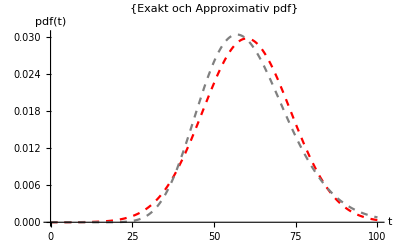

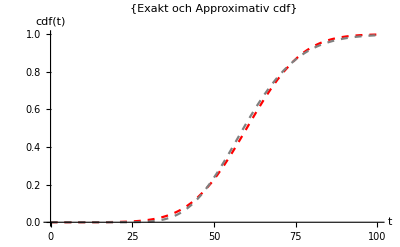

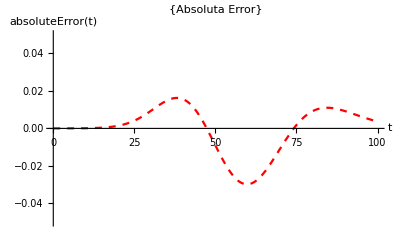

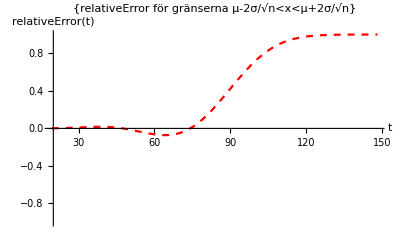

```mathematica
ClearAll["`*"]

(*Exakta fördelningen*)
λ = 1/3; (*förväntade tidsintervall*)
n = 20; (*antalet iid rvs*)

gamma =GammaDistribution[n, 1/λ];
Subscript[μ, exakt]  = Mean[gamma];
σ = StandardDeviation[gamma];

(*Approximativa distro*)
approxi = NormalDistribution[Subscript[μ, exakt] , σ ];

(*P("Absolut fel för X>x") = (1 - P("Exakta sannolikhet för X=<x")) -(1 - P("Approximativa sannolikhet för X=<x"))*)

Pexact[x_] :=N[ (1-CDF[gamma,x])];
Papprox[x_]:= N[ (1-CDF[approxi,x])];
absoluteError[x_] :=  Pexact[x] - Papprox[x] ;

relativeError[x_] := absoluteError[x]/Pexact[x]

(*Plotar pdf, där exakta funktionen är i grå mot normalapproximation svart*)
Plot[{PDF[approxi,t],PDF[gamma,t]},{t,0,100},PlotStyle->{{Dashed,Red},{Dashed,Gray}},PlotLabel->{"Exakt och Approximativ pdf"},AxesLabel->{HoldForm[t],HoldForm[pdf[t]]}, PlotRange->Full]

(*Plot av cdf, där exakta funktionen är i rött mot normalapproximation svart*)
Plot[{CDF[approxi,t],CDF[gamma,t]},{t,0,100},PlotStyle->{{Dashed,Red},{Dashed,Gray}},PlotLabel->{"Exakt och Approximativ cdf"},AxesLabel->{HoldForm[t],HoldForm[cdf[t]]}]

(*Plot av Absolut fel*)
Plot[{absoluteError[t]},{t,0,100},PlotRange -> {-0.05,.05},PlotStyle->{{Dashed,Red},{Dashed,Gray}},PlotLabel->{"Absoluta Error"},AxesLabel->{HoldForm[t],HoldForm[absoluteError[t]]}]

(*Plot av Relative Error*)
Plot[{relativeError[x]},{x, N[(Subscript[μ, exakt] -2σ) (√n)],N[(Subscript[μ, exakt] +2σ)/(√n)]},PlotRange -> {-1,1},PlotStyle->{{Dashed,Red},{Dashed,Gray}},PlotLabel->{"relativeError för gränserna μ-2σ/√n<x<μ+2σ/√n"},AxesLabel->{HoldForm[t],HoldForm[relativeError[t]]}]
```

#### Uppgift 2: Studera antalet av inkommande samtal under en timme.

Uppgiften: Plotta absolute och relative error av sannolikhet funktionen genom normal approximationen. Conclusion?

```mathematica
ClearAll["`*"]

(*Exakta fördelningen*)
```